```mathematica
Clear["Global`*"]
```

## Definitions & initial meshes for k, k+q vectors

```mathematica
a=2.46;(*a is given in units of 10^-10*)
b=(4π)/(√3*a); (*Magnitude of reciprocal vectors*)
b1=b*{(√3)/2.,1/2.}; (*Reciprocal vectors b1,b2*)
b2=b*{(-√3)/2.,1/2.};
b3=(b1+b2);
kk=1/3.(2  b1+b2);
kp=1/3.(b1-b2);
n=10;

(*kij the indices of the vectors in the k-mesh: *)
kij=Module[{sol},
sol=Table[{i,j},{i,-n+1,n},{j,Max[-n,-n-i]+1,Min[n,n-i]}];
Flatten[sol,1]
];

(*kqij contains the indices of the vectors in the k+q mesh: *)
kqij=Flatten[Table[
k=kij[[i]];
q=kij[[j]];
k+q 
,{i,1,Length[kij]},{j,1,Length[kij]}]
,1];


(*This function transltes from indices i,j to vectors: *)
IndexToVector[kij_]:=Module[{sol},
sol=Table[kij[[i]].(1/n{kk,kp}),{i,1,Length[kij]}]
];

(*Obtaining vectors for the  k and k+q meshes: *)
kmesh=IndexToVector[kij];
kqmesh=IndexToVector[kqij];



(*Cell benchmarks (laptop):
n=20 -> t=12.80s
n=40 -> t=191.8s
*)
```

## Plots: Initial meshes for k and k+q vectors

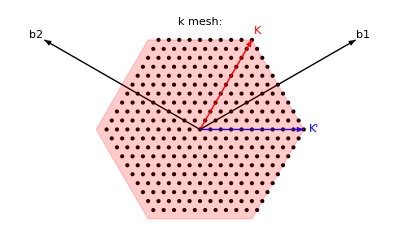

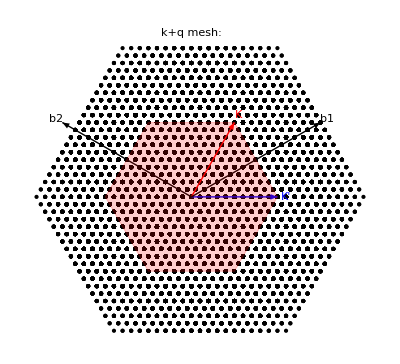

```mathematica
(*Drawing the contours and vectors of the 1BZ for the figures: *)
BZcontour = Polygon[{((4π)/(3a))*{-1,0},((4π)/(3a))*{(-1)/2,(√3)/2},((4π)/(3a))*{1/2,(√3)/2},((4π)/(3a))*{1,0},((4π)/(3a))*{1/2,(-√3)/2},((4π)/(3a))*{(-1)/2,(-√3)/2}}];
BZvectors =Graphics[{
Red,Arrow[{{0,0},kk}],
Blue,Arrow[{{0,0},kp}],
Black,Arrow[{{0,0},b1}],
Black,Arrow[{{0,0},b2}],
Black, Text["b1",b1*1.05],
Black, Text["b2",b2*1.05],
Red, Text["K",kk*1.1],
Blue, Text["K'",kp*1.1],
Red,Opacity[0.2],EdgeForm [Dashed],BZcontour
}];

(*Plotting the k mesh: *)
Show[Graphics[{
Text["k mesh:",0.6b3],
Point[kmesh],
PointSize[0.01]}],
BZvectors
]
(*Plotting the k+q mesh*)
Show[Graphics[{
Text["k+q mesh:",1.1b3],
Point[kqmesh],
PointSize[0.01]}],BZvectors
]
```

# Defining projection functions

```mathematica
(*The functions P1,P2,P3 give the projections of k along b1, b2, b3 (working with indices i,j)*)
P3[kij_]:=Module[{sol,n3},
i=kij[[All,1]];
n3=If[#>n,+1,
If[#<=-n,-1,0]
]& /@ i;
sol=TensorProduct[n3,{2n,-n}]
]
P2[kij_]:=Module[{sol,n2},
i=kij[[All,1]];
j=kij[[All,2]];
n2=MapThread[If[ #1 >0 && #2 <= -n  ,+1,
If[#2>n && #1<= 0, -1,0]
]& ,{ i,j}];

sol=TensorProduct[n2,{n,-2n}]
]
P1[kij_]:=Module[{sol,n1},
i=kij[[All,1]];
j=kij[[All,2]];
n1=MapThread[If[ #1+#2 > n && #1>0  ,+1,
If[#1+#2<=-n && #1<= 0, -1,0]
]& ,{ i,j}];
sol=TensorProduct[n1,{n,n}]
]


(*First we subtract projection along b3: *)
kqP3ij=kqij-P3[kqij];
(* ...then along b2: *)
kqP3P2ij=kqP3ij-P2[kqP3ij];
(* ...then along b1: *)
kqP3P2P1ij=kqP3P2ij-P1[kqP3P2ij];


(* Going from indices i,j to vectors: *)
{kqP3mesh, kqP3P2mesh,kqP3P2P1mesh}=Map[IndexToVector,{kqP3ij,kqP3P2ij,kqP3P2P1ij}];

(*Cell benchmarks (laptop):
n=20 -> t=
n=40 -> t=1134.69
*)
```

## Plots: Folding k+q vectors back to the 1BZ (showing one projection at a time)

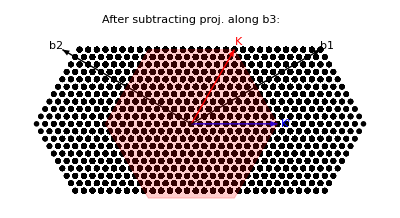

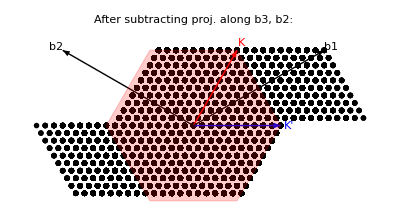

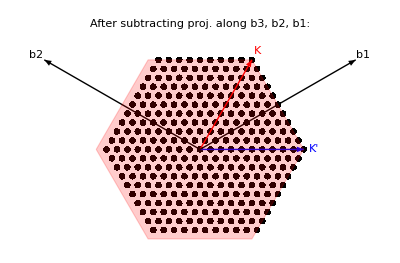

```mathematica
Show[Graphics[{PointSize[0.01],
Text["After subtracting proj. along b3:",0.7b3],
Point[kqP3mesh]}],
BZvectors
]

Show[Graphics[{PointSize[0.01],
Text["After subtracting proj. along b3, b2:",0.7b3],
Point[kqP3P2mesh]}],
BZvectors
]

Show[Graphics[{PointSize[0.01],
Text["After subtracting proj. along b3, b2, b1:",0.7b3],
Point[kqP3P2P1mesh]}],
BZvectors
]
```